```mathematica
ClearAll["Global`*"]
```

## N= 60

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=90
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten :=  3.05 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {89.3011} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {79.69} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {89.3011} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {89.3011} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {3.05984×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

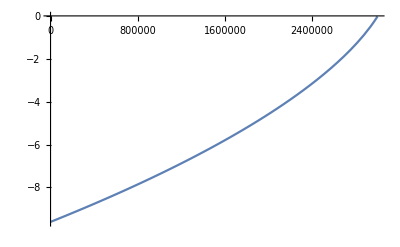

```mathematica
Plot[ϕ[t]-ϕend,{t,0,3 10^6},PlotRange->All]
```

```mathematica
tend
```

3.00318×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
ϕ[hc[0.05]]
```

80.3202

```mathematica
k:=0.00009
Timing[PS[k]]
```

{2.75,2.75347×10^-9}

```mathematica
k:=0.05
Timing[PS[k]]
```

{11.7969,2.11755×10^-9}

```mathematica
k:=0.002
Timing[r[k]]
```

{7.39063,0.0551449}

## Extracting PS(k) N=60

```mathematica
list =Parallelize[Table[{k,PS[k]},{k,0.0001,0.1,0.0001}]];
list1  = Parallelize[Table[{k,PS[k]},{k,0.1+0.01,2.5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data\\k_vs_PS(k)_mu=90.dat.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data\k_vs_PS(k)_mu=100.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PS(k) N =60

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=90.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot] + β/6 (Log[k/kpivot])^2),{AS,spec, α,β},k]
```

FittedModel[2.11149×10^-9 ⅇ^(-0.0898324-0.000100561 Log[20. k]^2) k^(-0.0307862-0.000266866 Log[20. k]-0.0000335682 Log[20. k]^2)]

```mathematica
Normal[%]
```

2.11149×10^-9 ⅇ^(-0.0898324-0.000100561 Log[20. k]^2) k^(-0.0307862-0.000266866 Log[20. k]-0.0000335682 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→2.11655×10^-9,spec→0.970013,α→-0.000533731,β→-0.000201409}

```mathematica
PPS[k_]:=2.1114856697382565*^-9 ⅇ^(-0.08983239015199773-0.00010056133043423965 Log[20. k]^2) k^(-0.030786246388654435-0.00026686559240034647 Log[20. k]-0.000033568196771782476 Log[20. k]^2)
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k] dPPS[k];
```

```mathematica
PPS[0.05]
```

2.11655×10^-9

```mathematica
nnS[0.002/0.05]
```

0.970127

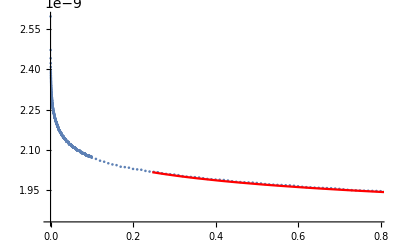

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1,plot2 }]
```

```mathematica
fit["RSquared"]
```

0.999999

## Extracting PT(k) N=60

```mathematica
list =Parallelize[Table[{k,PT[k]},{k,0.001,0.1,0.002}]];
list1  = Parallelize[Table[{k,PT[k]},{k,0.1+0.01,5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=90.dat.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data_PT\k_vs_PT(k)_mu=90.dat.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PT(k) N =60

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=90.dat.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot] + β/6 (Log[k/kpivot])^2),{AS,spec, α,β},k]
```

FittedModel[1.56415×10^-11 ⅇ^(-0.022819-4.31624×10^-6 Log[20. k]^2) k^(-0.00793119-0.000104823 Log[20. k]-1.4408×10^-6 Log[20. k]^2)]

```mathematica
Normal[%]
```

1.56415×10^-11 ⅇ^(-0.022819-4.31624×10^-6 Log[20. k]^2) k^(-0.00793119-0.000104823 Log[20. k]-1.4408×10^-6 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→1.56562×10^-11,spec→0.992383,α→-0.000209645,β→-8.64477×10^-6}

```mathematica
PPT[k_]:=1.5641525977105246*^-11 ⅇ^(-0.0228190028256812-4.316237523279386*^-6 Log[20. k]^2) k^(-0.007931190427095646-0.0001048225019857074 Log[20. k]-1.440795481419577*^-6 Log[20. k]^2)
dPPT[k_]=D[PPT[k],{k,1}];
nnT[k_]=k/PPT[k] dPPT[k];
```

```mathematica
PPT[0.05]
```

1.56562×10^-11

```mathematica
PPT[0.002]
```

1.60282×10^-11

```mathematica
nnT[0.002/0.05]
```

-0.0075706

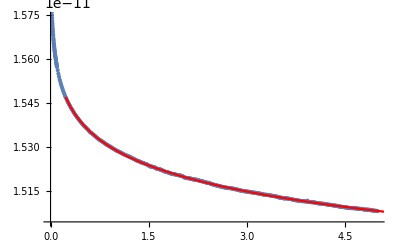

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPT[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1,plot2 }]
```

```mathematica
fit["RSquared"]
```

1.

## Calculation r(k) N =60

```mathematica
8 PPT[0.002]/PPS[0.002]
```

0.0550988

## N= 50

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-50==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=90
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N50.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten :=  2.27 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {89.3011} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {80.532} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {89.3011} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {89.3011} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

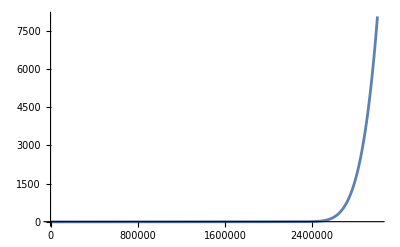

```mathematica
Plot[ϕ[t]-ϕend,{t,0,3 10^6},PlotRange->All]
```

```mathematica
tend
```

2.22401×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
ϕ[hc[0.05]]
```

81.2236

```mathematica
k:=0.00009
Timing[PS[k]]
```

{1.21875,3.00174×10^-9}

```mathematica
k:=0.05
Timing[PS[k]]
```

{7.8125,2.12833×10^-9}

```mathematica
k:=0.002
Timing[r[k]]
```

{5.84375,0.0683194}

## Extracting PS(k) N=50

```mathematica
list =Parallelize[Table[{k,PS[k]},{k,0.0001,0.1,0.0001}]];
(*list1  = Parallelize[Table[{k,PS[k]},{k,0.1+0.01,5,0.01}]];*)
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=90_N50.dat.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data_PS\k_vs_PS(k)_mu=90_N50.dat.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PS(k) N =50

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=90_N50.dat.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot] + β/6 (Log[k/kpivot])^2),{AS,spec, α,β},k]
```

FittedModel[2.12435×10^-9 ⅇ^(-0.10632-0.000433003 Log[20. k]^2) k^(-0.0358805-0.000130145 Log[20. k]-0.00014454 Log[20. k]^2)]

```mathematica
Normal[%]
```

2.12435×10^-9 ⅇ^(-0.10632-0.000433003 Log[20. k]^2) k^(-0.0358805-0.000130145 Log[20. k]-0.00014454 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→2.12683×10^-9,spec→0.964509,α→-0.000260291,β→-0.00086724}

```mathematica
PPS[k_]:=2.1243506270911926*^-9 ⅇ^(-0.10632028870525109-0.0004330032161594616 Log[20. k]^2) k^(-0.035880464853452816-0.0001301453360122741 Log[20. k]-0.00014454002448148267 Log[20. k]^2)
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k] dPPS[k];
```

```mathematica
PPS[0.05]
```

2.12683×10^-9

```mathematica
nnS[0.002/0.05]
```

0.964546

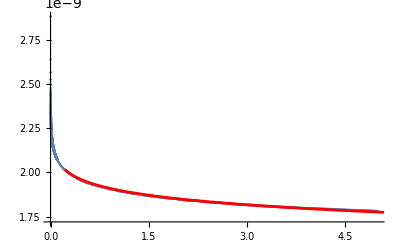

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1,plot2 }]
```

```mathematica
fit["RSquared"]
```

0.999994

## Extracting PT(k) N=50

```mathematica
list =Parallelize[Table[{k,PT[k]},{k,0.001,0.1,0.002}]];
list1  = Parallelize[Table[{k,PT[k]},{k,0.1+0.01,5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=90_N50.dat.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data_PT\k_vs_PT(k)_mu=90_N50.dat.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PT(k) N =50

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=90_N50.dat.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot] + β/6 (Log[k/kpivot])^2),{AS,spec, α,β},k]
```

FittedModel[1.97265×10^-11 ⅇ^(-0.0287865-0.0000121981 Log[20. k]^2) k^(-0.0100233-0.000138228 Log[20. k]-4.07184×10^-6 Log[20. k]^2)]

```mathematica
Normal[%]
```

1.97265×10^-11 ⅇ^(-0.0287865-0.0000121981 Log[20. k]^2) k^(-0.0100233-0.000138228 Log[20. k]-4.07184×10^-6 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→1.9751×10^-11,spec→0.990391,α→-0.000276456,β→-0.000024431}

```mathematica
PPT[k_]:=1.9726526319317702*^-11 ⅇ^(-0.028786534152818524-0.0000121981335747993 Log[20. k]^2) k^(-0.010023274622320192-0.00013822779030310236 Log[20. k]-4.071837020445098*^-6 Log[20. k]^2)
dPPT[k_]=D[PPT[k],{k,1}];
nnT[k_]=k/PPT[k] dPPT[k];
```

```mathematica
PPT[0.05]
```

1.9751×10^-11

```mathematica
PPT[0.002]
```

2.03451×10^-11

```mathematica
nnT[0.002/0.05]
```

-0.0095481

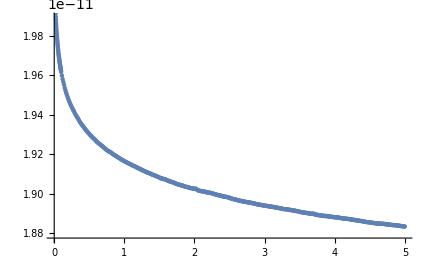

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1,plot2 }]
```

```mathematica
fit["RSquared"]
```

1.

## Calculation r(k) N =50

```mathematica
8*PPT[0.002]/PPS[0.002]
```

0.068029